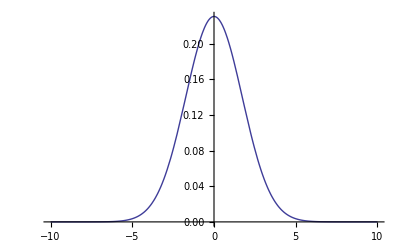

```mathematica
Plot[{(1/√(6*Pi))*E^(-(x^2/6))},{x,-10,10}]
```

```mathematica
∫_-Infinity^4 (1/0.886226925453/√(3*Pi))(1+x^2/3)^-2 ⅆx
```

0.985996

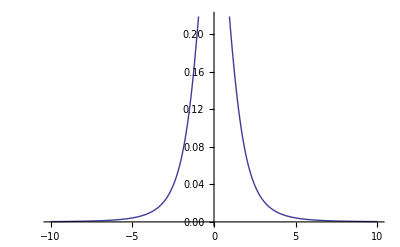

```mathematica
Plot[{(1/0.886226925453/√(3*Pi))(1+x^2/3)^-2},{x,-10,10}]
```

```mathematica
P2[z_]:=∫_0^z (1/0.886226925453/√(3*Pi))(1+x^2/3)^-2 ⅆx
```

```mathematica
P2[5]
```

0.492304

```mathematica
Plot[{P2[x]-.3},{x,0,10}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {0.000204286, 0, 0.000204286}.

NIntegrate::itraw: Raw object 0.000204286 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.204286, 0, 0.204286}.

NIntegrate::itraw: Raw object 0.204286 cannot be used as an iterator.

General::stop: Further output of NIntegrate :: itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {0.408368, 0, 0.408368}.

General::stop: Further output of Integrate :: ilim will be suppressed during this calculation.

-Graphics-

```mathematica
p2[x_]:=(1/0.886226925453/√(3*Pi))(1+x^2/3)^-2
```

```mathematica
p2[0]
```

0.367553

```mathematica
p2[1]
```

0.206748

```mathematica
P2[x_]:=x/15*p2[0]+4*x/15*p2[x/5]+2*x/15*p2[2*x/5]+4*x/15*p2[3*x/5]+2*x/15*p2[4*x/5]+x/15*p2[x]
```

```mathematica
P2[5]
```

0.481333

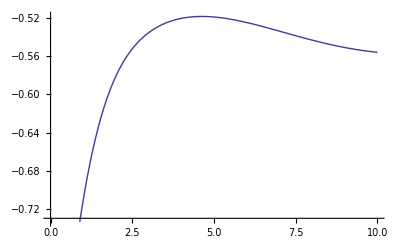

```mathematica
Plot[P2[x]-1,{x,0,10}]
```